Далее в блокноте:
	Ω[β, α] -- частота Раби
	ωR[β, α] -- частота перехода β→α
	ωD -- сдвинутая по Доплеру частота лазера 
	ρ[β, α] -- матричный элемент матрицы плотности
	e -- множество возбужденных состояний
	g -- множество ground состояний
	τ -- время жизни

```mathematica
ClearAll[ρ, α, β, γ, i, j, k, Ω, ωR, ρ0, e, g, τ];
```

```mathematica
g = {1,2};
e = {3,4};
nStates = Length@Join[g, e];
```

## Print eq

```mathematica
ClearAll[Eq2Print];
Eq2Print[eq_] := eq /. {
τ -> 1, 
Ω[β_, α_] :>   Subscript["Ω", ToString[β]<>ToString[α]], 
ωR[β_, α_] :> Subscript["ω", ToString[β]<>ToString[α]],
C[β_, α_] :> Subscript["C", ToString[β]<>ToString[α]],
ρ[β_, α_] :> Subscript["ρ", ToString[β]<>ToString[α]],
ωD :> "ω'",
ρRe[β_, α_] :> Subscript["ρ^re", ToString[β]<>ToString[α]],
ρIm[β_, α_] :> Subscript["ρ^im", ToString[β]<>ToString[α]]
};
```

## Релаксационная часть

```mathematica
ClearAll[LPart];
LPart[β_, α_] := -1/(2 τ)ρ0[β, α] /; MemberQ[g, α] && MemberQ[e, β];
LPart[β_, α_] := -1/τ ρ0[β, α]/;α== β && MemberQ[e, β];
LPart[β_, α_] := 1/τ Total@Map[ C[#, α]^2 ρ0[#, #]&, e] /; α == β && MemberQ[g, α];
LPart[β_, α_] := 0;
```

```mathematica
(* пример *)
n = 3;
Table[LPart[i, j], {i, 1, n}, {j, 1, n}] // MatrixForm // FullSimplify // Eq2Print
```

(C_31^2 ρ0[3,3]+C_41^2 ρ0[4,4] | 0 | 0
0 | C_32^2 ρ0[3,3]+C_42^2 ρ0[4,4] | 0
-1/2 ρ0[3,1] | -1/2 ρ0[3,2] | -ρ0[3,3])

## Атомарная часть

```mathematica
ClearAll[APart, ωR];
APart[β_, α_] := ℏ (ωR[β, α] - ω) ρ0[β, α] /; β ≠ α;
APart[β_, α_] := ℏ ωR[β, α] ρ0[β, α] /; β == α;
ωR[β_, α_] := 0 /; β == α;
```

```mathematica
(* пример *)
n = 2;
Table[APart[i, j], {i, 1, n}, {j, 1, n}] // MatrixForm // FullSimplify // Eq2Print
```

(0 | ℏ (-ω+ω_12) ρ0[1,2]
ℏ (-ω+ω_21) ρ0[2,1] | 0)

## Взаимодейтвие

```mathematica
ClearAll[IPart, Ω];
IPart[β_, α_] :=Sum[
ℏ Ω[β, j] Cos[φ]ρ0[j, α] - ρ0[β, j] ℏ Ω[j, α] Cos[φ]
,{j, 1, nStates}];
Ω[β_, α_] := 0 /; β== α;
(*Ω[α_, β_] := Ω[β, α] /; MemberQ[g, α] && MemberQ[e, β];*)
Ω[α_, β_] := Ω[β, α] /; α < β;
```

```mathematica
(* пример *)
n = 2;
Eq2Print@EqSimplify@IPart[1,1]
```

EqSimplify[-ℏ Cos[φ] Ω_21 ρ0[1,2]-ℏ Cos[φ] Ω_31 ρ0[1,3]-ℏ Cos[φ] Ω_41 ρ0[1,4]+ℏ Cos[φ] Ω_21 ρ0[2,1]+ℏ Cos[φ] Ω_31 ρ0[3,1]+ℏ Cos[φ] Ω_41 ρ0[4,1]]

## Приближения

Важно помнить, что считаем ρ[β1, β2] и ρ[α1, α2] малыми / не влияюшими на динамику.
Также для упрощения все слагаемые вида ρ[α, β] выразим как Conjugate[ρ[β, α]].

```mathematica
ClearAll[ρ0, ρ];
ρ0[i_, j_] := ρ[i, j]/; MemberQ[e,i]&& MemberQ[g,j];
ρ0[i_, j_] := 0 /; MemberQ[e,i]&& MemberQ[e,j]&& i ≠ j;
ρ0[i_, j_] := 0 /; MemberQ[g,i]&& MemberQ[g,j]&& i ≠ j;
ρ0[i_, j_] := Conjugate[ρ[j, i]]/; MemberQ[g,i]&& MemberQ[e,j];
ρ0[i_, j_] := ρ[i, j]/; i == j;
```

```mathematica
ρ0[1, 1]
ρ0[1, 2]
ρ0[2, 2]
```

ρ[1,1]

0

ρ[2,2]

## Всё вместе

```mathematica
ClearAll[Expandρ, globA, Re2Im];
globA = {Ω[x_, y_] ∈ Reals&& C[x_, y_] ∈ Reals && ωD ∈ Reals&& φ ∈ Reals && τ ∈ Reals && τ ≠ 0 && ℏ >0 && t >0 && ρIm[x_, y_] ∈ Reals && ρRe[x_, y_] ∈ Reals && ρIm[x_, x_] == 0 && ωR[x_, y_] ∈ Reals&& ω >0};
Re2Im = # /. {
ρ[a_, b_] - Re[ρ[a_, b_]]->ⅈ Im[ρ[a, b]],
Re[ρ[a_, b_]]-ρ[a_, b_]->-ⅈ Im[ρ[a, b]]
}&;
Expandρ[eq_] := eq/. {ρ[x_, y_]  -> ρRe[x, y] + ⅈ ρIm[x, y]};
EqSimplify[eq_] := FullSimplify[eq, Assumptions->globA] ;
```

```mathematica
ClearAll[MasterEq];
MasterEq[β_,α_] :=FullSimplify[ (APart[β, α]+IPart[β, α]+ⅈ ℏ LPart[β, α])/(ⅈ ℏ), Assumptions->globA, TransformationFunctions->{Automatic,Re2Im}];
```

```mathematica
MasterEq[1, 1]
```

(C[3,1]^2 ρ[3,3]+C[4,1]^2 ρ[4,4]+2 τ Cos[φ] (Im[ρ[3,1]] Ω[3,1]+Im[ρ[4,1]] Ω[4,1]))/τ

```mathematica
Eq2Print@MasterEq[1, 1]
```

C_31^2 ρ_33+C_41^2 ρ_44+2 Cos[φ] (Im[ρ_31] Ω_31+Im[ρ_41] Ω_41)

## Матрица диффура

```mathematica
VarsVec = {ρRe[1,1], ρRe[2,2], ρRe[3,3], ρRe[4, 4],ρIm[3, 1],ρIm[3, 2],ρIm[4, 1],ρIm[4, 2], ρRe[3, 1], ρRe[3, 2], ρRe[4, 1], ρRe[4, 2]};
VarsVecI = {{1, 1, 1}, {1, 2, 2},{1, 3,3}, {1, 4, 4},{2, 3,1}, {2, 3,2},{2, 4,1}, {2, 4,2}, {1, 3,1}, {1, 3, 2}, {1, 4,1}, {1, 4, 2}};
VarsVec // Eq2Print
```

{(ρ^re)_11,(ρ^re)_22,(ρ^re)_33,(ρ^re)_44,(ρ^im)_31,(ρ^im)_32,(ρ^im)_41,(ρ^im)_42,(ρ^re)_31,(ρ^re)_32,(ρ^re)_41,(ρ^re)_42}

```mathematica
EvolMatrix = Table[
Coefficient[
EqSimplify@{Re, Im}⟦VarsVecI⟦i⟧⟦1⟧⟧@Expand@Expandρ@MasterEq[Sequence@@(VarsVecI⟦i⟧⟦2;;3⟧)]
,VarsVec⟦j⟧]
, {i, 1, Length@VarsVecI}, {j, 1, Length@VarsVecI}];
```

```mathematica
(* вид уравнения*)
"∂_t "(VarsVec// MatrixForm )  ==((EvolMatrix /. {φ-> 0}) // MatrixForm )(VarsVec// MatrixForm ) // Eq2Print
```

∂_t  ((ρ^re)_11
(ρ^re)_22
(ρ^re)_33
(ρ^re)_44
(ρ^im)_31
(ρ^im)_32
(ρ^im)_41
(ρ^im)_42
(ρ^re)_31
(ρ^re)_32
(ρ^re)_41
(ρ^re)_42)==(0 | 0 | C_31^2 | C_41^2 | 2 Ω_31 | 0 | 2 Ω_41 | 0 | 0 | 0 | 0 | 0
0 | 0 | C_32^2 | C_42^2 | 0 | 2 Ω_32 | 0 | 2 Ω_42 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | -2 Ω_31 | -2 Ω_32 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | -2 Ω_41 | -2 Ω_42 | 0 | 0 | 0 | 0
-Ω_31 | 0 | Ω_31 | 0 | -1/2 | 0 | 0 | 0 | ω-ω_31 | Ω_21 | -Ω_43 | 0
0 | -Ω_32 | Ω_32 | 0 | 0 | -1/2 | 0 | 0 | Ω_21 | ω-ω_32 | 0 | -Ω_43
-Ω_41 | 0 | 0 | Ω_41 | 0 | 0 | -1/2 | 0 | -Ω_43 | 0 | ω-ω_41 | Ω_21
0 | -Ω_42 | 0 | Ω_42 | 0 | 0 | 0 | -1/2 | 0 | -Ω_43 | Ω_21 | ω-ω_42
0 | 0 | 0 | 0 | -ω+ω_31 | -Ω_21 | Ω_43 | 0 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Ω_21 | -ω+ω_32 | 0 | Ω_43 | 0 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | Ω_43 | 0 | -ω+ω_41 | -Ω_21 | 0 | 0 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | Ω_43 | -Ω_21 | -ω+ω_42 | 0 | 0 | 0 | -1/2) ((ρ^re)_11
(ρ^re)_22
(ρ^re)_33
(ρ^re)_44
(ρ^im)_31
(ρ^im)_32
(ρ^im)_41
(ρ^im)_42
(ρ^re)_31
(ρ^re)_32
(ρ^re)_41
(ρ^re)_42)

## Графики

```mathematica
Clear[n1, n2, n3, n4, c1, c2];
subs =  {ρRe[1,1] -> n1, ρRe[2,2]-> n2, ρRe[3,3]-> n3 , ρRe[4,4]-> n4, 
φ -> 0,C[3,1] -> c1,C[3,2] -> √(1-c1^2),C[4,1] -> c2,C[4,2] -> √(1-c2^2),Ω[3,1] -> ωr c1, Ω[3,2] -> ωr √(1-c1^2),Ω[4,1] -> ωr c2, Ω[4,2] -> ωr √(1-c2^2),Ω[2, 1]-> 0,Ω[4, 3]-> 0
, ωR[3,1] -> ω + Δω31+δ, ωR[3,2] -> ω + δ + Δω32
, ωR[4,1] ->  ω + δ + Δω41, ωR[4,2] -> ω + δ + Δω42};
EM = (EvolMatrix/.subs);
EM// MatrixForm  // Eq2Print
```

(0 | 0 | c1^2 | c2^2 | 2 c1 ωr | 0 | 2 c2 ωr | 0 | 0 | 0 | 0 | 0
0 | 0 | 1-c1^2 | 1-c2^2 | 0 | 2 √(1-c1^2) ωr | 0 | 2 √(1-c2^2) ωr | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | -2 c1 ωr | -2 √(1-c1^2) ωr | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | -2 c2 ωr | -2 √(1-c2^2) ωr | 0 | 0 | 0 | 0
-c1 ωr | 0 | c1 ωr | 0 | -1/2 | 0 | 0 | 0 | -δ-Δω31 | 0 | 0 | 0
0 | -√(1-c1^2) ωr | √(1-c1^2) ωr | 0 | 0 | -1/2 | 0 | 0 | 0 | -δ-Δω32 | 0 | 0
-c2 ωr | 0 | 0 | c2 ωr | 0 | 0 | -1/2 | 0 | 0 | 0 | -δ-Δω41 | 0
0 | -√(1-c2^2) ωr | 0 | √(1-c2^2) ωr | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -δ-Δω42
0 | 0 | 0 | 0 | δ+Δω31 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | δ+Δω32 | 0 | 0 | 0 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | δ+Δω41 | 0 | 0 | 0 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | δ+Δω42 | 0 | 0 | 0 | -1/2)

```mathematica
vv = {n1, n2, n3,n4, im31, im32, im41, im42, re31, re32, re41, re42};
sol = Solve[EM.vv == {0,0,0,0,0,0,0,0,0,0,0, 0} && n1 + n2 + n3 + n4== 1, vv]⟦1⟧;
 = (n1/. sol);
n2S = (n2/. sol);
n3S = (n3/. sol);
n4S = (n4/. sol);
```

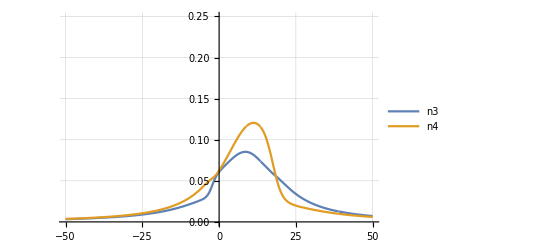

```mathematica
(*Manipulate[*)
subsN = {ωr-> 5,τ-> 1,Δω31-> 0,Δω32-> -20, Δω41-> 3, Δω42-> 3-20, c1 -> 0.9, c2 ->0.2};
n1M=  n1S/.subsN;
n2M = n2S /. subsN;
n3M = n3S /. subsN;
n4M = n4S /. subsN;
Plot[{n3M, n4M}, {δ, -50, 50}, PlotRange-> {Automatic, {0, 0.25}},PlotLegends->{"n3", "n4"}, GridLines->Automatic]
(*, {{ωr0, 5}, 0.1,20}, {c10, 0.9, 1}]*)
```